```mathematica
Needs["PiCbench`"]
```

## 1- Magnitudes

```mathematica
MagnitudeList[]
```

Variable | Value | Definition
$dx | 1 | $dx:=1
$nx | 1024 | $nx:=1024
$qp | 0.0004 | $qp:=0.0004
$mp | 0.0004 | $mp:=0.0004
$np | 3000 | $np:=3000
$ionMass | 1836.15 | $ionMass:=1836.15
$dt | 1 | $dt:=1
$a | 1 | $a:=1
$b | 1 | $b:=1
$c | 1 | $c:=1
$charSpeed | 0.5 | $charSpeed:=0.5
$charSpeedIons | 0.0116685 | $charSpeedIons:=($charSpeed)/(√($ionMass))
$lx | 1024 | $lx:=$dx $nx
$wp | 0.0342327 | $wp:=√(($np ($qp)^2 $a)/($lx $mp))
$debyeLength | 14.6059 | $debyeLength:=($charSpeed)/($wp)

```mathematica
$dx::usage
```

Length of cell size in the x dimenssion

```mathematica
PrintConditions[]
```

Small cell condition - ($dx<<$lx) - 1 << 1024

Small time-step condition - ($dt<<$wp^-1) - 1 << 29.2119

Big world condition - ($debyeLength<<$lx) - 14.6059 << 1024

{Null,Null,Null}

```mathematica
$charSpeed=10;
```

```mathematica
PrintConditions[]
```

Small cell condition - ($dx<<$lx) - 1 << 1024

Small time-step condition - ($dt<<$wp^-1) - 1 << 29.2119

Big world condition - ($debyeLength<<$lx) - 292.119 << 1024

{Null,Null,Null}

```mathematica
$charSpeed=0.5;
```

## 2- Initialization

```mathematica
?UniformParticles1D
```

Generates a uniform particle distribution in [0, lx] x [-vmax,vmax].

```mathematica
UniformParticles1D[lx->$lx,vmax->$charSpeed*2,np->10]
```

{{729.404,0.204395},{221.,-0.775899},{262.401,0.414552},{507.304,-0.137414},{158.416,0.855598},{565.833,0.692004},{150.684,0.0988992},{677.113,-0.892721},{566.948,0.755836},{461.136,-0.0336675}}

```mathematica
electrons=UniformParticles1D[vmax->$charSpeed*2];
```

```mathematica
ions=UniformParticles1D[vmax->$charSpeedIons*2];
```

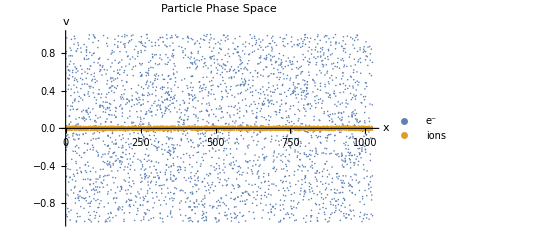

```mathematica
PhaseSpacePlot[{electrons,ions},PlotLegends->{"e^-","ions"}]
```

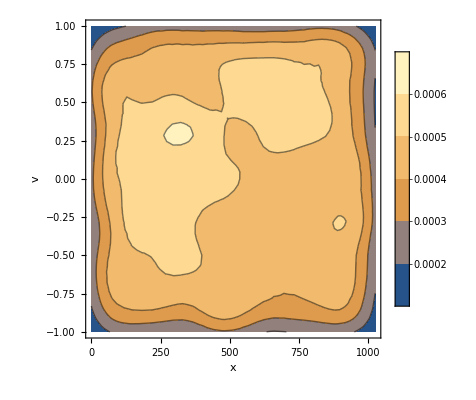

```mathematica
SmoothPhaseSpacePlot[electrons,PlotLegends->Automatic]
```

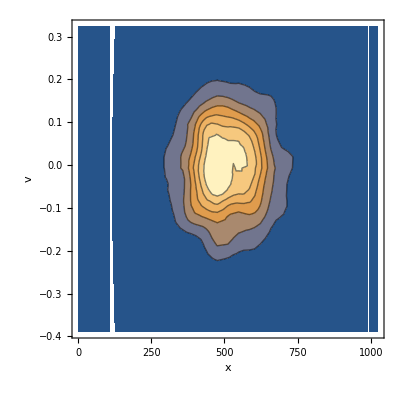
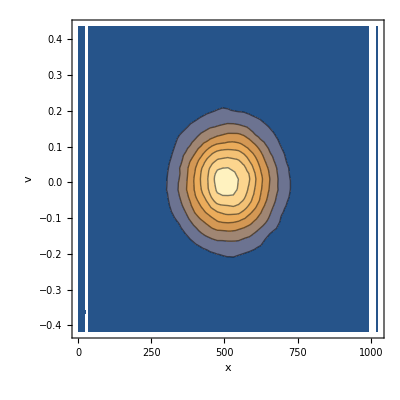

```mathematica
Table[SmoothPhaseSpacePlot[GaussianParticles1D[np->i]],{i,{1000,100000}}]
```

## 3- Particle to grid

```mathematica
?getRho1D
```

getRho1D[] returns a functions that calculates rho(particleList). Options include dx,nx,qc. Use with qc=1 to find number density.

A trick to see the code in a cleaned style:

```mathematica
Begin["PiCbench`Particle2Grid`Private`"];
Quiet[getRho1D[nx->"nx",dx->"dx",qp->"qp",Method->"First-order"],{Table::iterb}]
End[];
```

Function[{particles},Block[{rho,pos,x,PiCbench`Particle2Grid`Private`i},rho=Table[0.,{1+nx}];For[PiCbench`Particle2Grid`Private`i=1,PiCbench`Particle2Grid`Private`i≤Length[particles],PiCbench`Particle2Grid`Private`i++,x=particles⟦PiCbench`Particle2Grid`Private`i,1⟧;pos=Floor[x];rho⟦pos+1⟧+=pos+1-x;rho⟦pos+2⟧+=x-pos;];rho⟦1⟧+=rho⟦nx+1⟧;(Drop[rho,-1] qp)/dx]]

Use should be made by using a compiled function

```mathematica
getρ=FCompile[getRho1D[],{_Real},{2},CompilationTarget->"C",RuntimeOptions->"Speed"]
```

CompiledFunction[…]

Automatic benchmark of compilation:

```mathematica
TableForm[{BenchmarkFCompile[{getRho1D[],{_Real},{2}},{electrons},100],BenchmarkFCompile[{getRho1D[Method->"Zeroth-order"],{_Real},{2}},{electrons},100]},TableHeadings->{{"1st","0th"},{"None","WVM","C","CSpeed"}}]
```

| None | WVM | C | CSpeed
1st | 0.0233589 | 0.00052258 | 0.00017497 | 0.00005303
0th | 0.0137777 | 0.0003002 | 0.00013014 | 0.00006105

```mathematica
ρElectron=getρ[electrons];
```

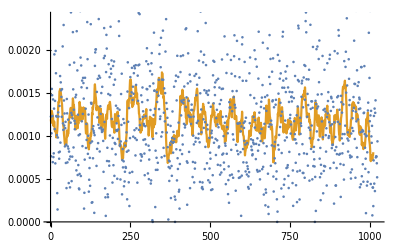

```mathematica
ListPlot[{ρElectron,DebyeMovingAverage[ρElectron]},Joined->{False,True}]
```

```mathematica
ρIon=getρ[ions];
```

## Solving Maxwell

```mathematica
getE=FCompile[GetE1D[],{_Real},{1},{{Re[__],_Real,1}},CompilationTarget->"C",RuntimeOptions->"Speed"];
```

```mathematica
eField=getE[(ρIon-ρElectron)];
```

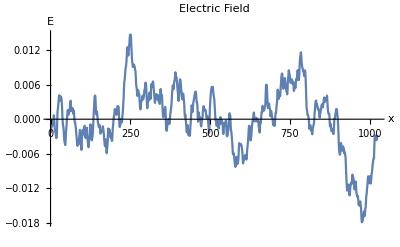

```mathematica
ListPlot[{eField},PlotLabel->"Electric Field",AxesLabel->{"x","E"},Joined->True]
```

The efficiency of Fourier methods rely on using FFT techniques.
Test speed using two configurations, one allowing for FFT

```mathematica
With[{b1n=1000,b2n=1024},
b1getρ=FCompile[getRho1D[nx->b1n],{_Real},{2},CompilationTarget->"C",RuntimeOptions->"Speed"];
b2getρ=FCompile[getRho1D[nx->b2n],{_Real},{2},CompilationTarget->"C",RuntimeOptions->"Speed"];
b1e=b1getρ[UniformParticles1D[lx->b1n,vmax->$charSpeed*2]];
b1i=b1getρ[UniformParticles1D[lx->b1n,vmax->$charSpeedIons*2]];
b2e=b2getρ[UniformParticles1D[lx->b2n,vmax->$charSpeed*2]];
b2i=b2getρ[UniformParticles1D[lx->b2n,vmax->$charSpeedIons*2]];
{BenchmarkFCompile[{GetE1D[nx->b1n,Method->"Fourier"],{_Real},{1},{{Re[__],_Real,1}}},{b1i-b1e},2000],
BenchmarkFCompile[{GetE1D[nx->b2n,Method->"Fourier"],{_Real},{1},{{Re[__],_Real,1}}},{b2i-b2e},2000],
BenchmarkFCompile[{GetE1D[nx->b1n,Method->"Fourier-diff"],{_Real},{1},{{Re[__],_Real,1}}},{b1i-b1e},2000],BenchmarkFCompile[{GetE1D[nx->b2n,Method->"Fourier-diff"],{_Real},{1},{{Re[__],_Real,1}}},{b2i-b2e},2000]}
]//TableForm[#,TableHeadings->{{"1000 - Fourier","1024 - Fourier","1000 - Fourier-diff","1024 - Fourier-diff"},{"None","WVM","C","CSpeed"}}]&
```

| None | WVM | C | CSpeed
1000 - Fourier | 0.000349802 | 0.0000874865 | 0.000086133 | 0.000086477
1024 - Fourier | 0.000350278 | 0.000059417 | 0.0000595095 | 0.000059784
1000 - Fourier-diff | 0.000354928 | 0.000125409 | 0.000123518 | 0.000124643
1024 - Fourier-diff | 0.000296299 | 0.0000948895 | 0.000094534 | 0.000092351